```mathematica
D[n^x,x]
```

n^x Log[n]

```mathematica
Integrate[ n^x Log[n], {x,0,s}]
```

-1+n^s

```mathematica
D[n^x,n]
```

n^(-1+x) x

```mathematica
D[n^-x,x]
```

-n^-x Log[n]

```mathematica
D[ (1^-s+2^-s+3^-s+4^-s)^k,s]
```

(1+2^-s+3^-s+4^-s)^(-1+k) k (-2^-s Log[2]-3^-s Log[3]-4^-s Log[4])

```mathematica
Limit[(1+2^-s+3^-s+4^-s)^k Log[1+2^-s+3^-s+4^-s],k->t]
```

(1+2^-s+3^-s+4^-s)^t Log[1+2^-s+3^-s+4^-s]

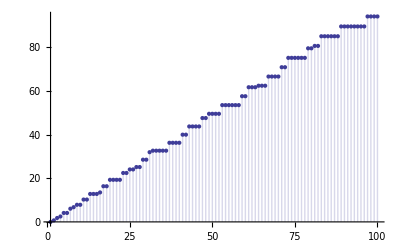

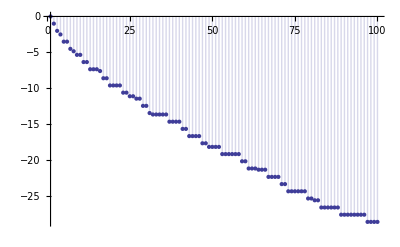

```mathematica
ff[n_]:=MoebiusMu[n]
G2[n_, k_,s_] := Sum[ j^-s ff[j]G2[Floor[n/j],k-1,s],{j,2,n}];G2[n_,0,s_]:=1
G1[n_,z_,s_]:=Sum[ Binomial[z,k]G2[n,k,s],{k,0,Log[2,n]}]
DiscretePlot[Limit[D[G1[n,z,s]/z,s]/.s->0,z->0],{n,1,100}]
DiscretePlot[Limit[D[G1[n,z,0],z],z->0],{n,1,100}]
```

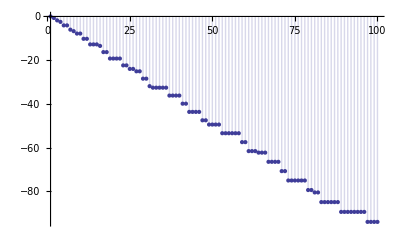

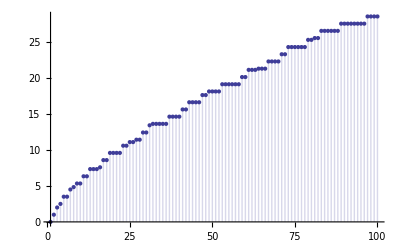

```mathematica
ff[n_]:=1
G2[n_, k_,s_] := Sum[ j^-s ff[j]G2[Floor[n/j],k-1,s],{j,2,n}];G2[n_,0,s_]:=1
G1[n_,z_,s_]:=Sum[ Binomial[z,k]G2[n,k,s],{k,0,Log[2,n]}]
DiscretePlot[Limit[D[G1[n,z,s]/z,s]/.s->0,z->0],{n,1,100}]
DiscretePlot[Limit[D[G1[n,z,0],z],z->0],{n,1,100}]
```

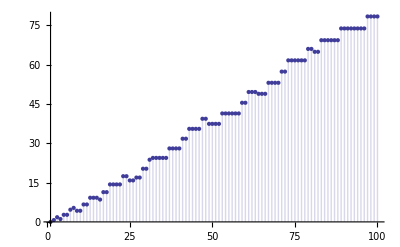

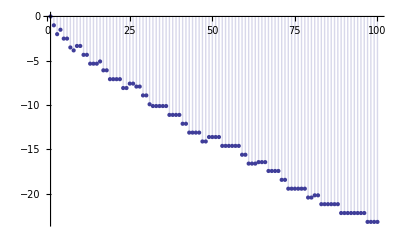

```mathematica
ff[n_]:=LiouvilleLambda[n]
G2[n_, k_,s_] := Sum[ j^-s ff[j]G2[Floor[n/j],k-1,s],{j,2,n}];G2[n_,0,s_]:=1
G1[n_,z_,s_]:=Sum[ Binomial[z,k]G2[n,k,s],{k,0,Log[2,n]}]
DiscretePlot[Limit[D[G1[n,z,s]/z,s]/.s->0,z->0],{n,1,100}]
DiscretePlot[Limit[D[G1[n,z,0],z],z->0],{n,1,100}]
```

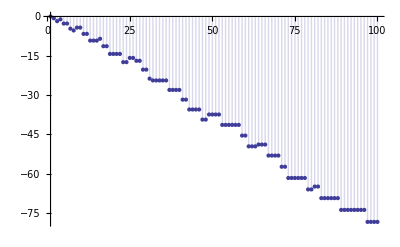

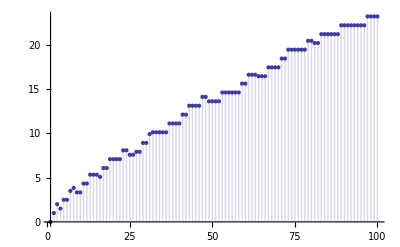

```mathematica
ff[n_]:=Abs[MoebiusMu[n]]
G2[n_, k_,s_] := Sum[ j^-s ff[j]G2[Floor[n/j],k-1,s],{j,2,n}];G2[n_,0,s_]:=1
G1[n_,z_,s_]:=Sum[ Binomial[z,k]G2[n,k,s],{k,0,Log[2,n]}]
DiscretePlot[Limit[D[G1[n,z,s]/z,s]/.s->0,z->0],{n,1,100}]
DiscretePlot[Limit[D[G1[n,z,0],z],z->0],{n,1,100}]
```